This file contains functions used by ERACS to plot the pareto front.

# Functions

```mathematica
<<".mathrc";
```

```mathematica
colorData = ColorData[3];
```

```mathematica
dpi = 72;
```

```mathematica
myMarkerSize = .4 dpi;
```

```mathematica
circle[] := Graphics[Circle[], ImageSize -> myMarkerSize]
```

```mathematica
box[] := Graphics[{EdgeForm[Black], Transparent, Rectangle[]}, ImageSize->myMarkerSize]
```

```mathematica
plotFront[points_, index_:1] := Module[{p1, p2, p3},
p1 = ListPlot[points, Joined ->True, PlotLegends -> LineLegend[{"front"}], PlotRangePadding -> Scaled[.1]];
p2 = ListPlot[Map[List, points], PlotStyle -> Map[colorData, Range[Length[points]]],
PlotMarkers -> {Automatic, Medium}, PlotLegends -> Map[ToString,Range[Length[points]]]];
p3 = ListPlot[{points[[index]]},
PlotMarkers -> {circle[]}, PlotLegends -> {"current"}, PlotStyle -> Black];
Show[p1,p2, p3]]
```

```mathematica
plotPoint[point_, opts:OptionsPattern[Options[ListPlot]]] := ListPlot[{point},PlotMarkers -> {Automatic, Medium}, Evaluate[FilterRules[{opts},Options[ListPlot]]]]
```

```mathematica
plotFrontAndPoint[points_, index_, lastPoint_] :=
Show[{plotFront[points, index], plotPoint[lastPoint, PlotLegends ->{"previous"}, PlotStyle -> {colorData[ 1+Length[points]]}]}, PlotRange -> All]
```

```mathematica
exportPDF[filename_, expr_] := Export[filename, expr,"PDF", ImageSize ->2  pdfImageSize]
```

```mathematica
mathematicaToSexp[x_RGBColor] := ("#"<>mathematicaToSexp[Apply[List,Append[x,1.]]])
```

```mathematica
mathematicaToSexp[x_List] := ("(" <> StringJoin[Riffle[Map[mathematicaToSexp,x], " "]]<> ")")
```

```mathematica
mathematicaToSexp[x_Real] := ToString[x]
```

```mathematica
mathematicaToSexp[x_Integer] := ToString[x]
```

```mathematica
path[points_] := Line[points]
```

```mathematica
box[pos_, dims_] := {Transparent, Cuboid[pos - dims/2, pos + dims/2]}
```

```mathematica
plotRobotPathAndObstacles[points_, obstacles_] :=
Graphics3D[{path[points], Map[box@@#&,obstacles], {PointSize[Large],Green, Opacity[0.5], Point[points[[-1]]]}},Axes->{True, False, True},AxesLabel->{"x","y","z"},ViewPoint->{0,Infinity,0},ViewVertical->{0,0,-1}, PlotRangePadding -> 2]
```

```mathematica
plotFitnessTimeSeries[results_] := ListPlot[Transpose[Map[Function[{input}, Map[ {input[[1]], #}&,input[[2]]]],results[[All,{1,3}]]]], Joined -> True, PlotRange -> All, AxesLabel -> {"generation", "fitness"}, AxesOrigin -> {1, 0}]
```

# Demo

```mathematica
Dynamic[plotRobotPathAndObstacles[{{-0.42561861872673,0.815069675445557,1.84015762805939},{-0.41815122961998,0.829686939716339,1.83243930339813},{-0.411038994789124,0.845922112464905,1.8249192237854},{-0.403638243675232,0.861606776714325,1.81552934646606},{-0.396173357963562,0.877667367458344,1.80691683292389},{-0.387779831886292,0.894819617271423,1.79818117618561},{-0.379807621240616,0.911753237247467,1.78891897201538},{-0.370917946100235,0.928771793842316,1.77897751331329},{-0.363547414541245,0.945104241371155,1.77140426635742},{-0.355890810489655,0.962910950183868,1.7651275396347},{-0.348549544811249,0.979689538478851,1.75709283351898},{-0.3413365483284,0.997335970401764,1.74744844436646},{-0.33428955078125,1.01468908786774,1.73652958869934},{-0.327039062976837,1.03280341625214,1.72269690036774},{-0.320372670888901,1.05110991001129,1.70667552947998}}, {{{0,1,-10}, {1,1,1}},
{{0, 1, -5}, {10,1,1}}}]]
```

```mathematica
Dynamic[Graphics3D[{path[{{1,1,-1},{2,2,1},{3,3,-1},{4,4,1}}],
box[{0,0,0}, {1,1,1}]}, Axes -> {True, False, True}, AxesLabel -> {"x", "y", "z"}]]
```

```mathematica
exportPDF["path-plot.pdf",Graphics3D[{path[{{-0.0253487136214972,1.00817763805389,0.181168854236603},{-0.0161291677504778,1.02566242218018,0.172572240233421},{-0.00676033133640885,1.04400062561035,0.163045942783356},{0.00324325961992145,1.0616934299469,0.151699468493462},{0.011848384514451,1.0788494348526,0.138777449727058},{0.0178895760327578,1.09289968013763,0.123955070972443},{0.0204286016523838,1.10191190242767,0.105577759444714},{0.0362350679934025,1.16575658321381,0.0971855372190475},{0.0508939176797867,1.25194191932678,0.0840362086892128},{0.0466832369565964,1.31302404403687,0.0638626888394356},{0.0188884176313877,1.34766161441803,0.0156778674572706},{-0.00405020080506802,1.20635282993317,-0.0148862600326538}}]},Axes->True,AxesLabel->{"x","y","z"}]]
```

```mathematica
exportPDF["test.pdf", Graphics3D[{path[{{1,1,-1},{2,2,1},{3,3,-1},{4,4,1}}],
box[{0,0,0}, {1,1,1}]}, Axes -> True, AxesLabel -> {"x", "y", "z"}]]
```

test.pdf

```mathematica
SystemOpen["test.pdf"]
```

```mathematica
SetDirectory["/Users/shane/School/uvm/CSYS-395-evolutionary-robotics/noweb-eracs"];
```

```mathematica
exportColorData[filename_] := Export[filename,"(define colors #"<>mathematicaToSexp[Map[colorData, Range[10]]] <> ")", "Text"]
```

```mathematica
"what" >> "colors.scm"
```

```mathematica
exportColorData["colors.scm"];
```

```mathematica
Directory[]
```

/Users/shane/School/uvm/CSYS-395-evolutionary-robotics/noweb-eracs

```mathematica
mathematicaToSexp[Map[colorData, Range[10]]]//FullForm
```

"(#(0. 0. 0. 1.) #(0.996078 0.360784 0.027451 1.) #(0.996078 0.988235 0.0352941 1.) #(0.541176 0.713725 0.027451 1.) #(0.145098 0.435294 0.384314 1.) #(0.00784314 0.509804 0.929412 1.) #(0.152941 0.113725 0.490196 1.) #(0.470588 0.262745 0.584314 1.) #(0.890196 0.0117647 0.490196 1.) #(0.905882 0.027451 0.129412 1.))"

```mathematica
SetOptions[InputNotebook[],AutoGeneratedPackage->Automatic]
```

```mathematica
Dynamic[Show[plotFrontAndPoint[testFront, 2, -10 {-1,-1}], AxesLabel -> {"hi", "bye"}, AxesOrigin -> {0, 0}]]
```

```mathematica
Dynamic[plotPoint[{1,3}]]
```

```mathematica
testFront = 10{{1, 2}, {3,6}, {5, 9}}
```

{{10,20},{30,60},{50,90}}

```mathematica
Dynamic[plotFront[testFront, 3]]
```

```mathematica
Dynamic[Show[plotFront[testFront], AxesLabel -> {"hi", "bye"}]]
```

```mathematica
results = Import["run2/exp1-trial1/results.m"]
```

{{{1,12,{-0.0247998}},{1,2,{-0.211763}},{1,4,{-0.121844}},{1,3,{-0.153889}},{1,11,{-0.0298947}},{1,9,{-0.0517239}},{1,8,{-0.0578939}},{1,1,{-0.231577}},{1,6,{-0.0766132}},{1,10,{-0.0453977}},{1,5,{-0.110337}},{1,7,{-0.0649858}}},«98»,{{100,1,{-0.371371}},{100,1,{-0.371371}},{100,1,{-0.371371}},{100,1,{-0.371371}},«5»,{100,1,{-0.371371}},{100,1,{-0.371371}},{100,1,{-0.371371}}}}

```mathematica
results2 = {{{1, 1, {1, 2}}}, {{10, 2, {3, 5}}}}
```

{{{1,1,{1,2}}},{{10,2,{3,5}}}}

```mathematica
Transpose[Map[Function[{input}, Map[ {input[[1]], #}&,input[[2]]]],Flatten[results2,1][[All,{1,3}]]]]
```

{{{1,1},{10,3}},{{1,2},{10,5}}}

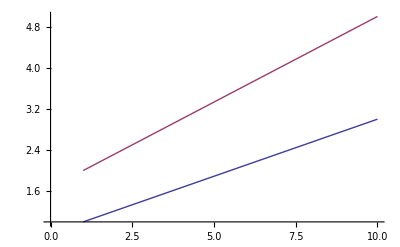

```mathematica
ListPlot[%99, Joined -> True]
```

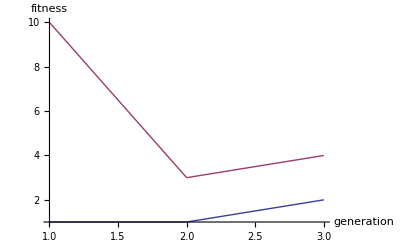

```mathematica
ListPlot[Map[{#[[1]], Sequence@@#[[2]]}&,Flatten[results2,1][[All,{1,3}]]], Joined -> True, PlotRange -> All, AxesLabel -> {"generation", "fitness"}]
```

```mathematica
(* sdf *)
```

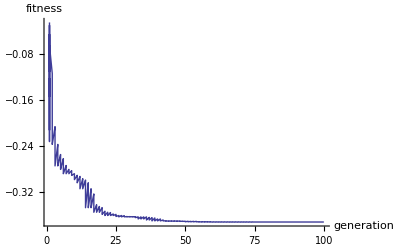

```mathematica
plotFitnessTimeSeries[Flatten[results,1]]
```

```mathematica
results3 = {{2,1,{-0.118770812499568}},{2,2,{-0.0859484364250073}},{2,3,{-0.0821600600881641}},{2,4,{-0.0745411813687041}},{1,3,{-0.0591417080332803}},{1,4,{-0.038307546587095}},{1,1,{-0.0859484364250073}},{1,2,{-0.0745411813687041}}};
```